```mathematica
This file exports 2 things.
1)  [BP]+[BPR] vs time (converted from the fluoroscence data)
2) The initial [BL] concentrations that are extracted from the experimental data
```

Exporting normalized [MPR] + [PR] for :B1P29-5/P5-6

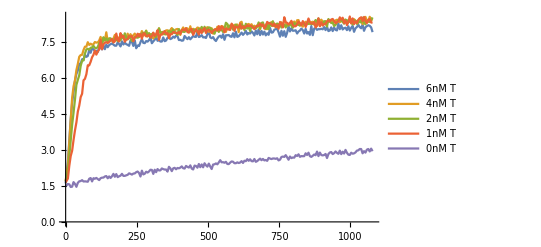

Exporting normalized [MPR] + [PR] for :B1P28-5/P5-7

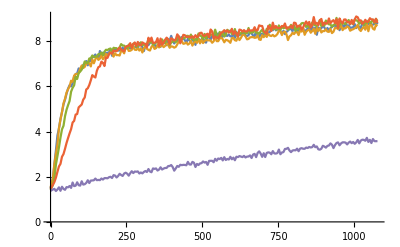

Exporting normalized [MPR] + [PR] for :B1P27-5/P5-8

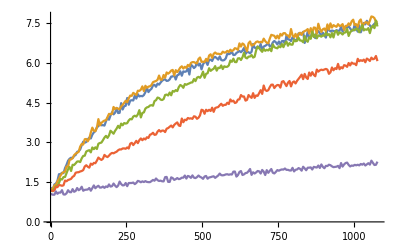

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["4. Discard Pathway"];
(*Plate1: B1, Plate2: B1a, Plate3:B1b*)
files={"20211214 DP plate1.xlsx","20211215 DP plate2.xlsx","20211216 DP plate3.xlsx"};
satred=Import["Sat_red.wl"];
(*fname is the file index of interest*)
For[fname=1,fname<=1(*Length[files]*),fname++,
(*Change these variables*)
tend=1100;(*final time of interest*)

Po=50;(*proofreader concentration*)
Ptype=1;(*1 means P29-5, 2 means P28-5, 3 means P27-5, 4 means P27-4*)
printall=0;
(*These variables remain constant more or less*)
injinfo=0;(*If injinfo =0, use conc before injection and time as avg of before and after, else use conc after injection and time as after injection*)
forward=1;(*1 if reaction forward going BP+RQ->BPR+Q, 0 otherwise*)
skip=0;(*skip timesteps after injection or not*)
X1corr=0;(*If 1, subtract sample X1 readings, else not*)
FRQ=691.03;(*Fl Alexa density of RQ*)
FBPR=8261.9;(*Fl Alexa density of BPR*)
FBP=8993;(*Fl Cy3 of BP*)
FC3BPR=8178.8;(*Cy3 value for BPR*)
w1=1;(*Changes weight on point before injection*)
w2=0;(*changes weight on point after injection*)
data=Import[files[[fname]],{"Sheets","Table All Cycles"}];

(*Extract relevant data*)
For[i=1,i<=Length[data],i++,
If[data[[i]][[1]]=="Content",Break[]]];
data=data[[i;;,2;;]];
(* 
data is as follows;
Time[min] Sample X1 Sample X2 Sample X3 Sample X4 Sample X5 Sample X6...
0 8983 9948 9248 9686 9373 9062
0.53 8696 9316 10039 9228 9138 9028
0.92 8647 9180 9539 9510 9125 9608
1.3 8820 9767 9968 9609 9353 9411
......
*)

(*Stores the legends in this variable*)
samplename=data[[1]][[2;;]];
legend={};(*will remove samples of insignificance from samplename array and be used as the legend list*)
For[i=1,i<=Length[samplename],i++,
If[samplename[[i]]=="Control C1"||samplename[[i]]=="Control C2"||samplename[[i]]=="Control C3"||samplename[[i]]=="Positive control P"||samplename[[i]]=="Negative control N",,
AppendTo[legend,samplename[[i]]];
]]

(*Extract column number of Poitive and Negative control (and extra conrols if exist). Also extract column number of Sample X1 and row number of Alexa and Cy3 Injection*);
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C3"||data[[1]][[i]]=="Negative control N",Break[]]];iC3=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C2",Break[]]];iC2=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C1"||data[[1]][[i]]=="Positive control P",Break[]]];iC1=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Sample X1",Break[]]];iS0=i;
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="n.a.",c++;If[c==2,Break[]]]];inj0=i;(*first injection row number*)
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="n.a.",c++;If[c==3,Break[]]]];inj=i;(*second injection row number*)

(*Functions defined for further data processing*)
f[x_]:=0;
cut[x_,t_]:=(For[i=1,i<=Length[x[[1]]],i++,If[x[[1]][[i]][[1]]>t,Break[]];];ret={};
For[j=1,j<=Length[x],j++,AppendTo[ret,x[[j]][[1;;Min[i-1,Length[x[[j]]]-1]]]]];
Return[ret];);


dnew=Array[f,Length[data[[1]]]-1];(*Stoes raw Alexa data*)
dnewtem=dnew;(*Stores raw Cy3 data*)
dnewfl=Array[f,Length[data[[1]]]-4];(*Stores Alexa normalized data*)
dnewfltem=dnewfl;(*Stores all Cy3 normalized data*)
(***************************************************************************************)
(*Create a concentration array where each element stores a table of {time,fluoroscence} after injection for the different samples including +ve and -ve controls*)
For[i=2,i<=Length[data[[1]]],i++,dnew[[i-1]]=data[[2;;,{1,i}]];];
(*Find the second Inj. point and save the row number where the time before 2nd Inj. is 0. *)
c=1;For[i=1,i<=Length[dnew[[1]]],i++,If[c==3,Break[]];If[dnew[[1]][[i]][[2]]=="n.a.",c++];
If[c==3,For[j=i-1,j>=1,j--,If[dnew[[1]][[j]][[1]]==0.,save=j;Break[];]]]
];

inj=inj-save+1;

(*Extract Cy3 signal and define time, conc at the injection poin: dnew*)
For[i=2,i<=Length[data[[1]]],i++,
dnew[[i-1]]=data[[save+1;;,{1,i}]](*Stores all datapoint of Alexa signal*);
If[dnew[[i-1]][[inj-1]][[2]]=="n.a.",If[injinfo==0,dnew[[i-1]][[inj-1]][[2]]=w1*dnew[[i-1]][[inj-2]][[2]]+w2*dnew[[i-1]][[inj]][[2]]],dnew[[i-1]][[inj-1]][[2]]=dnew[[i-1]][[inj]][[2]]];
If[dnew[[i-1]][[inj-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnew[[i-1]][[inj-1]][[1]]=w1*dnew[[i-1]][[inj-2]][[1]]+w2*dnew[[i-1]][[inj]][[1]],dnew[[i-1]][[inj-1]][[1]]=dnew[[i-1]][[inj]][[1]]];
]];

(*Extract Alexa signal: dnewtem*)
For[i=2,i<=Length[data[[1]]],i++,
dnewtem[[i-1]]=data[[2;;save,{1,i}]](*Stores all datapoint of Alexa signal*);
If[dnewtem[[i-1]][[inj0-1]][[2]]=="n.a.",If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0-2]][[2]]],dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0]][[2]]];
If[dnewtem[[i-1]][[inj0-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0-2]][[1]],dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0]][[1]]];
]];

concT={6,4,2,1,0};
a2={};For[i=1,i<=Length[concT],i++,
AppendTo[a2,ToString[concT[[i]]]<>"nM T"];];

If[printall==1,Print["Alexa Signal:"]];
s1=ListPlot[dnewtem[[1;;5]],Joined->True,PlotLegends->a2];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];

(*Collect fluoroscence data from Cy3 to estimate initial BP*)
s1=ListPlot[cut[dnew[[1;;5]],800],Joined->True,PlotLegends->a2,PlotRange->All];
If[printall==1,Print["Cy3 Signal:"]];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];

Clear[na];
drawAl=dnewtem;
drawCy=dnew;



(*Select injection point*)
na=inj-1;
(**)

(*Update the conc array by subtracting control C3 values from conc and using normalized time. Note inj-1 is impt bec inj was calculated on whole data, then the first name row was removed and inj. line was removed too*)
c=1; For[i=1,i<=Length[dnew],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1,Continue[],
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-dnew[[i]][[na]][[1]],If[j==na,dnew[[i]][[j-1]][[2]]-dnew[[iC3-1]][[j-1]][[2]],dnew[[i]][[j]][[2]]-dnew[[iC3-1]][[j]][[2]]](*-dnew[[iS0-1]][[j]][[2]]*)},{j,na,Length[dnew[[i]]]-1,1}];]];
dnew=dnewfl;

na=inj0-1;
(*dnewtem=cut[dnewtem,tend];*)
(*subtract control C3 frm BP data*)
c=1; For[i=1,i<=Length[dnewtem],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1,Continue[],
dnewfltem[[c++]]=Table[{dnewtem[[i]][[j]][[1]]-dnewtem[[i]][[na]][[1]],If[j==na,dnewtem[[i]][[j-1]][[2]]-dnewtem[[iC3-1]][[j-1]][[2]],dnewtem[[i]][[j]][[2]]-dnewtem[[iC3-1]][[j]][[2]]]},{j,na,Length[dnewtem[[i]]]-1,1}];]];

dnewtem=dnewfltem;

If[printall==1,Print["Normalized Alexa signal"]];
s1=ListPlot[dnewtem[[1;;5]],Joined->True,PlotLegends->a2,BaseStyle->FontSize[8],Frame->True,FrameLabel->{"Time[min]","Fluoroscence"},FrameStyle->Thick];
If[printall==1,Print[s1]];
If[printall==1,Print["Normalized Cy3 signal"]];
s1=ListPlot[dnew[[1;;5]],Joined->True,PlotLegends->a2,BaseStyle->FontSize[8],Frame->True,FrameLabel->{"Time[min]","Fluoroscence"},FrameStyle->Thick,PlotRange->All];
If[printall==1,Print[s1]];

dnormAl=dnewtem;
dnormCy=dnew;

(*Export Normalized Alexa and Cy3 signal*)
bname="";
If[fname==1,bname="B1"];
If[fname==2,bname="B1a"];
If[fname==3,bname="B1b"];

data={dnewtem[[1]][[1;;,1]]};data2={dnew[[1]][[1;;,1]]};
For[i=1,i<=5,i++,
str=bname<>"P29-5";
AppendTo[data,dnewtem[[i]][[1;;,2]]];AppendTo[data2,dnew[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];
data={dnewtem[[1]][[1;;,1]]};data2={dnew[[1]][[1;;,1]]};
For[i=11,i<=15,i++,
str=bname<>"P28-5";
AppendTo[data,dnewtem[[i]][[1;;,2]]];AppendTo[data2,dnew[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];
data={dnewtem[[1]][[1;;,1]]};data2={dnew[[1]][[1;;,1]]};
For[i=21,i<=25,i++,
str=bname<>"P27-5";
AppendTo[data,dnewtem[[i]][[1;;,2]]];AppendTo[data2,dnew[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];
data={dnewtem[[1]][[1;;,1]]};data2={dnew[[1]][[1;;,1]]};
For[i=31,i<=35,i++,
str=bname<>"P27-4";
AppendTo[data,dnewtem[[i]][[1;;,2]]];AppendTo[data2,dnew[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];




(*Alexa analysis*)

(*This function returns the fluoroscent curves at {0,0} and retunrs the set of fluoroscent values at t=0 before normalization*)
clean[x_]:=(AO=x;store={};
For[ik=1,ik<=Length[x],ik++,
AO[[ik]]=Table[{x[[ik]][[j]][[1]],x[[ik]][[j]][[2]]-x[[ik]][[1]][[2]]},{j,1,Length[x[[ik]]]}];
AppendTo[store,x[[ik]][[1]][[2]]];
];
Return[{AO,store}];
);


(*Convert fluoroscence to concentrations*);
concRQ={};(*Will store list of initial [BL] concentrations*)
concBPR={};
concBPRi={};
For[i=1,i<=Length[dnewtem],i++,
FRQi=satred[[fname]][[Quotient[i-1,10]+1]]*FRQ;
(*Take value from saturation curves*)
XX=clean[dnewtem][[2]];
cBPRi=(XX[[i]]-FRQi)/FBPR;
AppendTo[concBPRi,cBPRi];
For[j=1,j<=Length[dnewtem[[i]]],j++,
dnewtem[[i]][[j]][[2]]=(dnewtem[[i]][[j]][[2]]-FRQi)/(FBPR);
];];


emp={};
concBPRf={};
For[i=1,i<=5,i++,
AppendTo[emp,Table[{dnewtem[[i]][[j]][[1]],0.5*(dnewtem[[i]][[j]][[2]]+dnewtem[[i+5]][[j]][[2]])},{j,1,Length[dnewtem[[i]]],1}]];
AppendTo[concBPRf,0.5*(concBPRi[[i]]+concBPRi[[i+5]])];
];
For[i=11,i<=15,i++,
AppendTo[emp,Table[{dnewtem[[i]][[j]][[1]],0.5*(dnewtem[[i]][[j]][[2]]+dnewtem[[i+5]][[j]][[2]])},{j,1,Length[dnewtem[[i]]],1}]];
AppendTo[concBPRf,0.5*(concBPRi[[i]]+concBPRi[[i+5]])];
];
For[i=21,i<=25,i++,
AppendTo[emp,Table[{dnewtem[[i]][[j]][[1]],0.5*(dnewtem[[i]][[j]][[2]]+dnewtem[[i+5]][[j]][[2]])},{j,1,Length[dnewtem[[i]]],1}]];
AppendTo[concBPRf,0.5*(concBPRi[[i]]+concBPRi[[i+5]])];
];
For[i=31,i<=35,i++,
AppendTo[emp,Table[{dnewtem[[i]][[j]][[1]],0.5*(dnewtem[[i]][[j]][[2]]+dnewtem[[i+5]][[j]][[2]])},{j,1,Length[dnewtem[[i]]],1}]];
AppendTo[concBPRf,0.5*(concBPRi[[i]]+concBPRi[[i+5]])];
];
(*concRQ for P29-5*)emp[[1;;5]];
(*concRQ for P28-5*)emp[[6;;10]];
(*conc RQ for P27-5*)emp[[11;;15]];
(*conc RQ for P27-4*)emp[[16;;20]];


emp2=emp;


(*Export the [BP]+[BPR] concentration with time for the 3 starting monomers. Current pipeline exports this in the folder named "4. Discard pathway"*)

Print["Exporting normalized [MPR] + [PR] for :", bname, "P29-5/P5-6"];
Export["Data\\"<>bname<>"P29-5.wl",emp[[1;;5]]];


s1=ListPlot[cut[emp[[1;;5]],tend],PlotLegends->a2,Joined->True];
Print[s1];

Print["Exporting normalized [MPR] + [PR] for :", bname, "P28-5/P5-7"];
Export["Data\\"<>bname<>"P28-5.wl",emp[[6;;10]]];

s1=ListPlot[cut[emp[[6;;10]],tend],Joined->True];
Print[s1];

Print["Exporting normalized [MPR] + [PR] for :", bname, "P27-5/P5-8"];
Export["Data\\"<>bname<>"P27-5.wl",emp[[11;;15]]];

s1=ListPlot[cut[emp[[11;;15]],tend],Joined->True];
Print[s1];

(*Print["Exportitng concBL and normalized [MPR] + [PR] for :", bname, "P27-4"];*)
Export["Data\\"<>bname<>"P27-4.wl",emp[[16;;20]]];

(*Cy3 analysis to extract concentration of [BT],[B1aT],[B1bT]. At longer times we have [MP]+[MPR], the signal should be a representation of [BL];*)
For[i=1,i<=Length[dnew],i++,
dnew[[i]]=Table[{dnew[[i]][[j]][[1]],dnew[[i]][[j]][[2]]/FC3BPR(*-concBPRi[[i]]*FC3BPR)/FC3BPR*)},{j,1,Length[dnew[[i]]],1}]];
(*dnew stores the concentration converted from fluoroscence*)

emp={};
For[i=1,i<=5,i++,
AppendTo[emp,Table[{dnew[[i]][[j]][[1]],0.5*(dnew[[i]][[j]][[2]]+dnew[[i+5]][[j]][[2]])},{j,1,Length[dnew[[i]]],1}]]];
For[i=11,i<=15,i++,
AppendTo[emp,Table[{dnew[[i]][[j]][[1]],0.5*(dnew[[i]][[j]][[2]]+dnew[[i+5]][[j]][[2]])},{j,1,Length[dnew[[i]]],1}]]];
For[i=21,i<=25,i++,
AppendTo[emp,Table[{dnew[[i]][[j]][[1]],0.5*(dnew[[i]][[j]][[2]]+dnew[[i+5]][[j]][[2]])},{j,1,Length[dnew[[i]]],1}]]];
For[i=31,i<=35,i++,
AppendTo[emp,Table[{dnew[[i]][[j]][[1]],0.5*(dnew[[i]][[j]][[2]]+dnew[[i+5]][[j]][[2]])},{j,1,Length[dnew[[i]]],1}]]];


(*Extracting conc generated from Cy3 signal*)
data={emp[[1]][[1;;,1]]};
For[i=1,i<=5,i++,
str=bname<>"P29-5.wl";
AppendTo[data,emp[[i]][[1;;,2]]]];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];
data={emp[[1]][[1;;,1]]};
For[i=6,i<=10,i++,
str=bname<>"P28-5.wl";
AppendTo[data,emp[[i]][[1;;,2]]];];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];
data={emp[[1]][[1;;,1]]};
For[i=11,i<=15,i++,
str=bname<>"P27-5.wl";
AppendTo[data,emp[[i]][[1;;,2]]];];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];

(*concRQ for P29-5*)emp[[1;;5]];
(*concRQ for P28-5*)emp[[6;;10]];
(*conc RQ for P27-5*)emp[[11;;15]];
(*conc RQ for P27-4*)emp[[16;;20]];



f[x_]:=0;

(*Extract the relevant concetrations*)
(*Initial conc of BL for the 4 proofreaders*)
concBL295=Array[f,5];
concBL285=Array[f,5];
concBL275=Array[f,5];
concBL274=Array[f,5];

(*For each plate, calculate the mean value of B1, B1a, B1b. This will be the starting [BT]*)
For[i=1,i<=5,i++,
concBL295[[i]]=Mean[emp[[1;;5]][[i]][[-10;;,2]]]-concBPRf[[i]]];
For[i=1,i<=5,i++,
concBL285[[i]]=Mean[emp[[6;;10]][[i]][[-10;;,2]]]-concBPRf[[i+5]]];
For[i=1,i<=5,i++,
concBL275[[i]]=Mean[emp[[11;;15]][[i]][[-10;;,2]]]-concBPRf[[i+10]]];
For[i=1,i<=5,i++,
concBL274[[i]]=Mean[emp[[16;;20]][[i]][[-10;;,2]]]-concBPRf[[i+15]]];


(*Subtract the proofreader concentration by [PR]i and export*)
pi[x_]:=Po;ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i]]];Export["Conc\\P\\"<>bname<>"P29-5.wl",ss];

ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+5]]];
Export["Conc\\P\\"<>bname<>"P28-5.wl",ss];

pi[x_]:=Po;ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+10]]];
Export["Conc\\P\\"<>bname<>"P27-5.wl",ss];

pi[x_]:=Po;ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+15]]];
Export["Conc\\P\\"<>bname<>"P27-4.wl",ss];


pi[x_]:=satred[[fname]][[1]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i]]];Export["Conc\\RQ\\"<>bname<>"P29-5.wl",ss];

pi[x_]:=satred[[fname]][[2]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+5]]];Export["Conc\\RQ\\"<>bname<>"P28-5.wl",ss];

pi[x_]:=satred[[fname]][[3]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+10]]];Export["Conc\\RQ\\"<>bname<>"P27-5.wl",ss];

pi[x_]:=satred[[fname]][[4]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]-concBPRf[[i+15]]];Export["Conc\\RQ\\"<>bname<>"P27-4.wl",ss];

conc={6,4,2,1,0};
qs=ListPlot[dnew[[1;;5]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->40,ImageSize->2000,PlotRange->All,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]]},{Style[ToString[NumberForm[conc[[1]],3]]<>"nM T",FontSize->30],Style[ToString[NumberForm[conc[[2]],3]]<>"nM T",FontSize->30],Style[ToString[NumberForm[conc[[3]],3]]<>"nM T",FontSize->30],Style[ToString[NumberForm[conc[[4]],3]]<>"nM T",FontSize->30],
Style[ToString[NumberForm[conc[[5]],3]]<>"nM T",FontSize->30]}]];
Export["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\SI\\Discard_pathway_Cy3.pdf",qs];

Export["Conc\\BL\\"<>bname<>"P29-5.wl",concBL295];
Export["Conc\\BPR\\"<>bname<>"P29-5.wl",concBPRf[[1;;5]]];
Export["Conc\\BL\\"<>bname<>"P28-5.wl",concBL285];
Export["Conc\\BPR\\"<>bname<>"P28-5.wl",concBPRf[[6;;10]]];
Export["Conc\\BL\\"<>bname<>"P27-5.wl",concBL275];
Export["Conc\\BPR\\"<>bname<>"P27-5.wl",concBPRf[[11;;15]]];
Export["Conc\\BL\\"<>bname<>"P27-4.wl",concBL274];
Export["Conc\\BPR\\"<>bname<>"P27-4.wl",concBPRf[[16;;20]]];
(*s1=ListPlot[emp[[15;;20]]];
Print[s1];
*)
(*Export the initial [BT] concentration used in the template recovery reaction. Current pipeline exports this in the folder named "4. Discard Pathway"*)


SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["4. Discard Pathway"];
satred=Import["Sat_red.wl"];
For[i=1,i<=4,i++,
satred[[fname]][[i]]=satred[[fname]][[i]]-Mean[concBPRi[[(i-1)*10+1;;10*i]]];
];
Export["Sat_red2.wl",satred];


]
```

```mathematica
Now, export data as pdf for SI.
```

{12,23,24,25,26,27,28,29,30,31,32,33}

{Positive Control,Negative Control,Sample X1,Sample X2,Sample X3,Sample X4,Sample X5,Sample X6,Sample X7,Sample X8,Sample X9,Sample X10}

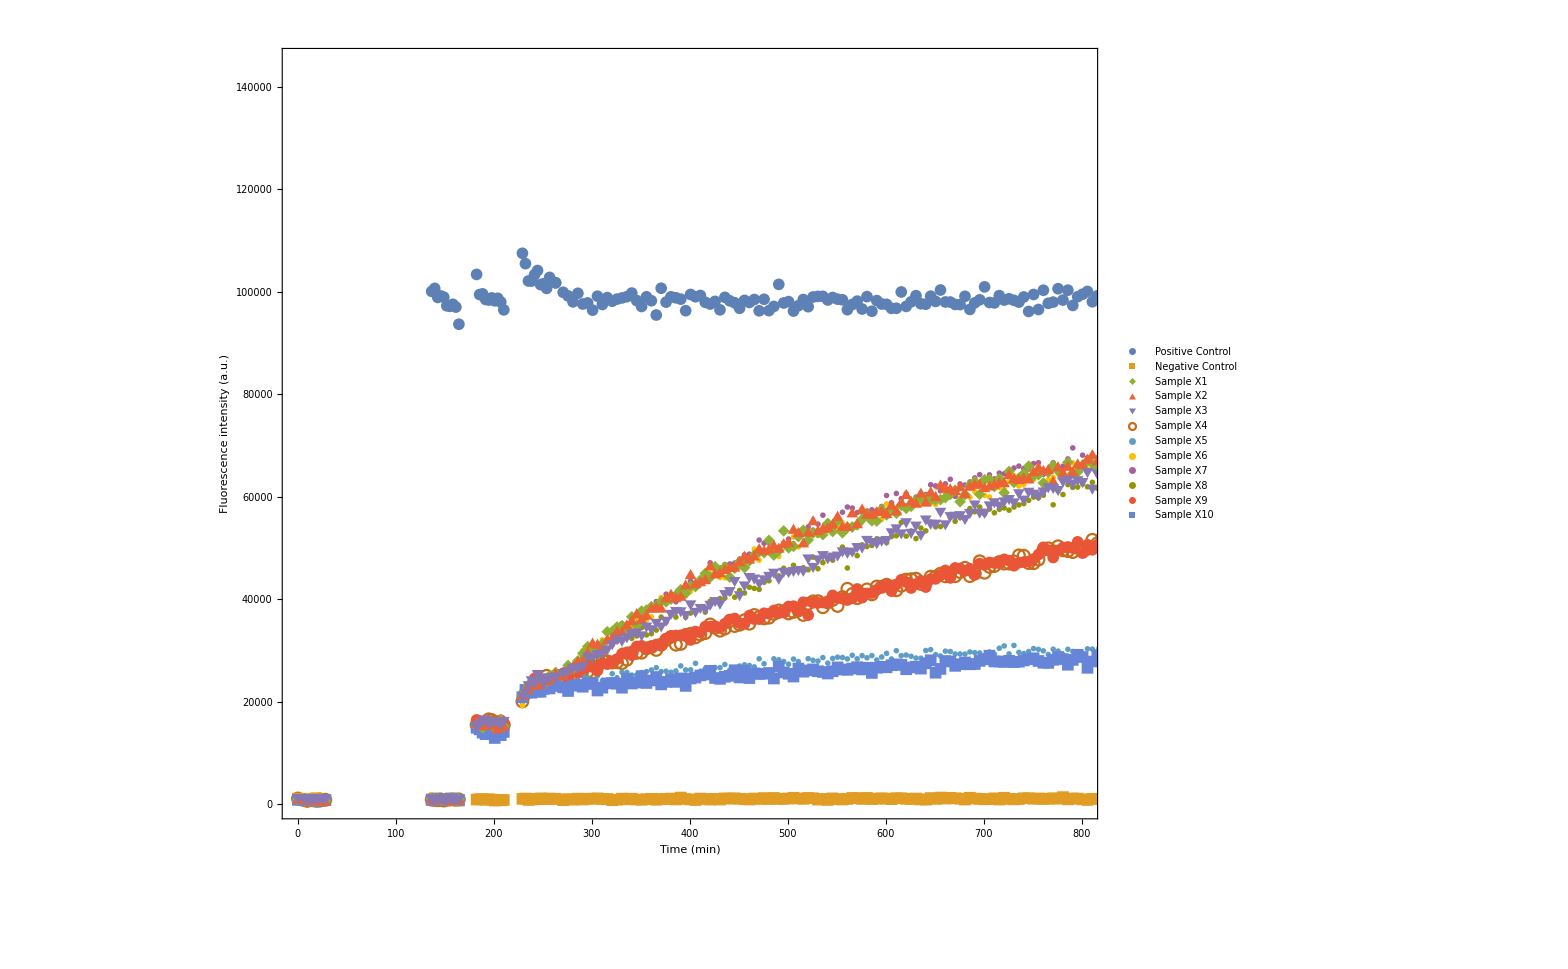

SI\DP_Alexa_raw.pdf

```mathematica
siz=10;
fntsz=35;
list={12,23,24,25,26,27,28,29,30,31,32,33}
concV={"Positive Control","Negative Control","Sample X1","Sample X2","Sample X3","Sample X4","Sample X5","Sample X6","Sample X7","Sample X8","Sample X9","Sample X10"}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[drawAl[[list]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz],Style[concV[[6]],FontSize->fntsz,Thickness[0.1]],Style[concV[[7]],FontSize->fntsz,Thickness[0.1]],Style[concV[[8]],FontSize->fntsz,Thickness[0.1]],Style[concV[[9]],FontSize->fntsz,Thickness[0.1]],Style[concV[[10]],FontSize->fntsz,Thickness[0.1]],Style[concV[[11]],FontSize->fntsz,Thickness[0.1]],Style[concV[[12]],FontSize->fntsz,Thickness[0.1]]},LegendLayout->{"Column",1}],Joined->False,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,12},PlotRange->{{0,800},All}]
Export["SI\\DP_Alexa_raw.pdf",qs]
```

{11,12,24,25,26,27,28,29,30,31,32,33}

{Positive Control,Negative Control,Sample X1,Sample X2,Sample X3,Sample X4,Sample X5,Sample X6,Sample X7,Sample X8,Sample X9,Sample X10}

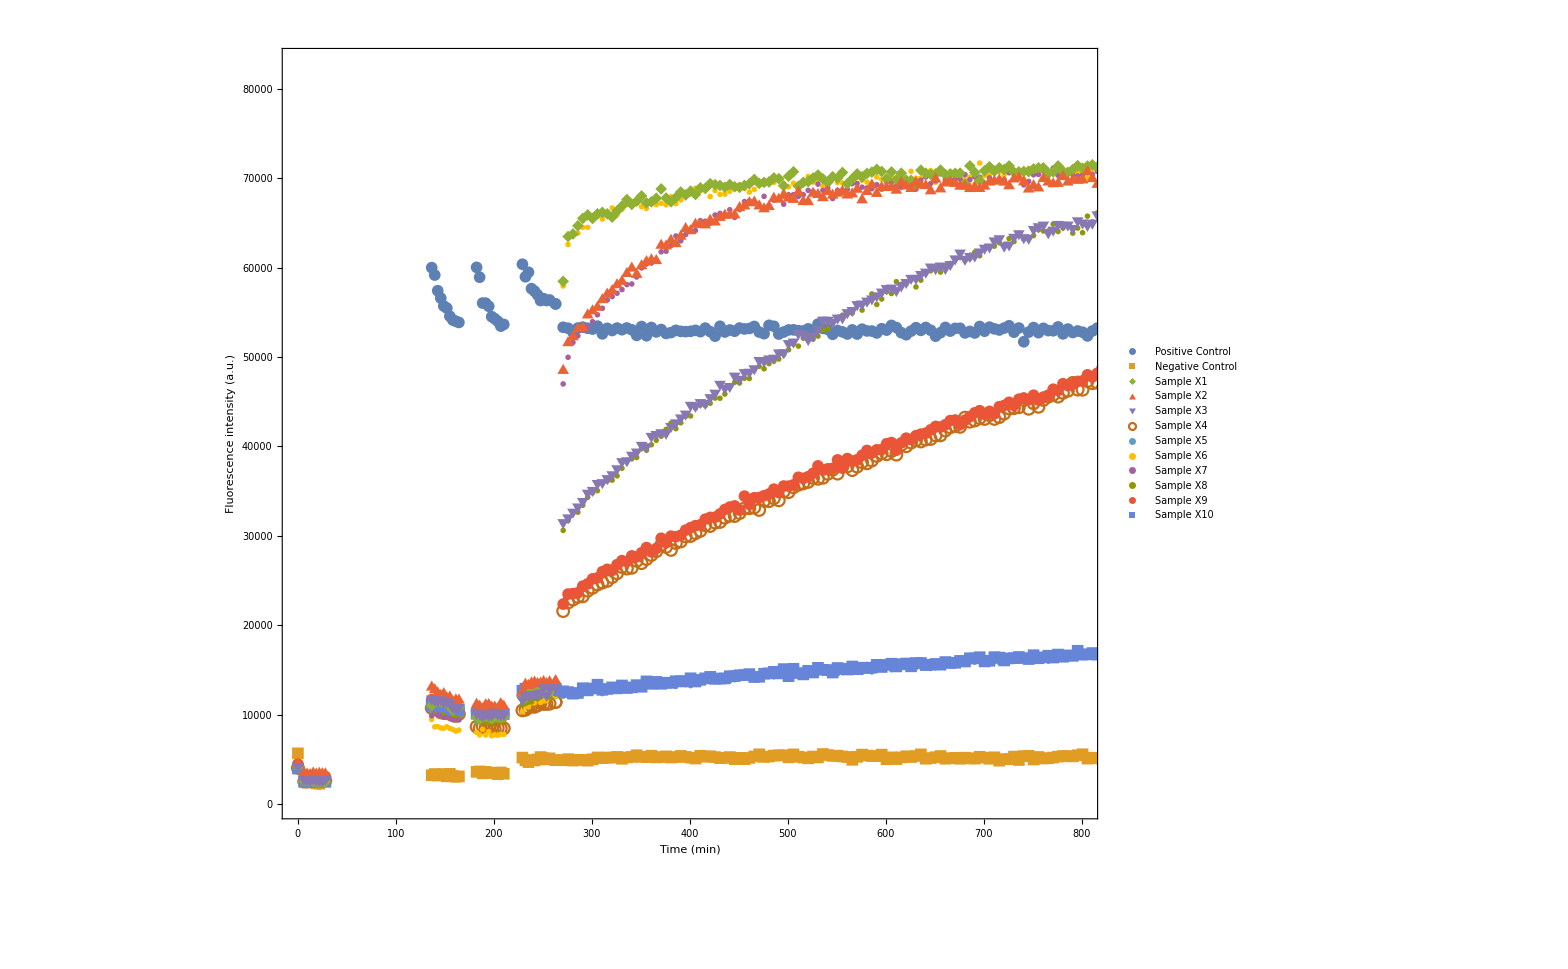

SI\DP_Cy3_raw.pdf

```mathematica
siz=10;
fntsz=35;
list={11,12,24,25,26,27,28,29,30,31,32,33}
concV={"Positive Control","Negative Control","Sample X1","Sample X2","Sample X3","Sample X4","Sample X5","Sample X6","Sample X7","Sample X8","Sample X9","Sample X10"}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[drawCy[[list]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz],Style[concV[[6]],FontSize->fntsz,Thickness[0.1]],Style[concV[[7]],FontSize->fntsz,Thickness[0.1]],Style[concV[[8]],FontSize->fntsz,Thickness[0.1]],Style[concV[[9]],FontSize->fntsz,Thickness[0.1]],Style[concV[[10]],FontSize->fntsz,Thickness[0.1]],Style[concV[[11]],FontSize->fntsz,Thickness[0.1]],Style[concV[[12]],FontSize->fntsz,Thickness[0.1]]},LegendLayout->{"Column",1}],Joined->False,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,12},PlotRange->{{0,800},All}]
Export["SI\\DP_Cy3_raw.pdf",qs]
```

{11,12,24,25,26,27,28,29,30,31,32,33}

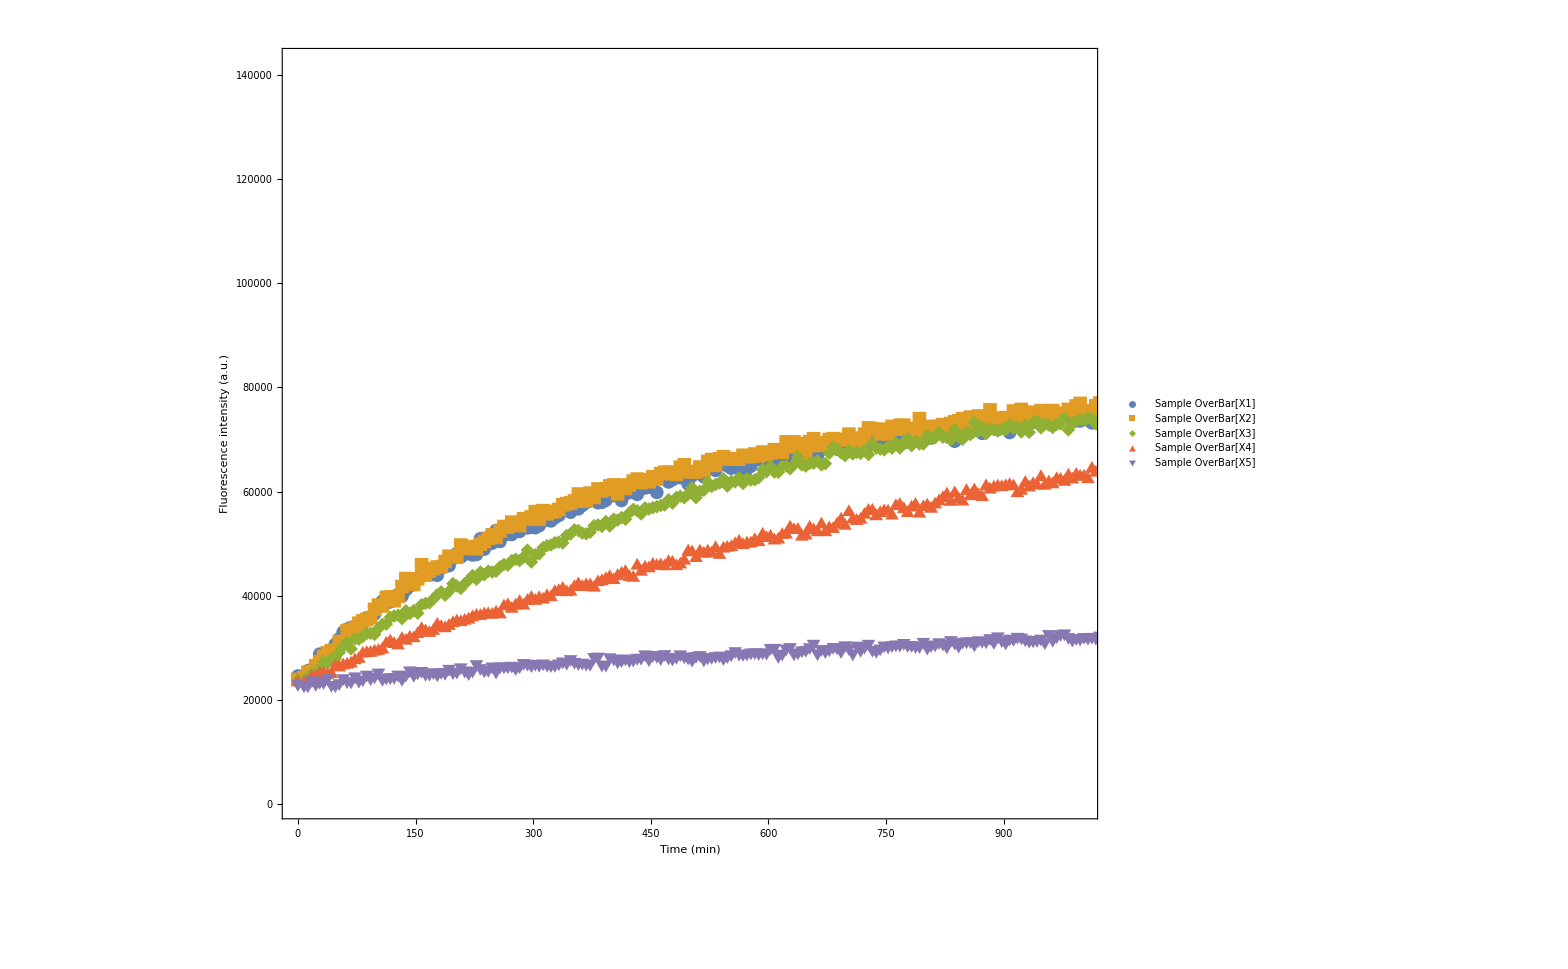

SI\DP_Cy3_norm.pdf

```mathematica
mean[x_]:=
(a1=x[[1;;5]];
For[i=1,i<=5,i++,
For[j=1,j<=Length[x[[i]]],j++,
a1[[i]][[j]][[1]]=x[[i]][[j]][[1]];
a1[[i]][[j]][[2]]=(x[[i]][[j]][[2]]+x[[i+5]][[j]][[2]])*0.5
]];
Return[a1];
)
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
list={11,12,24,25,26,27,28,29,30,31,32,33}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[mean[dnormAl[[21;;30]]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\DP_Cy3_norm.pdf",qs]
```

{11,12,24,25,26,27,28,29,30,31,32,33}

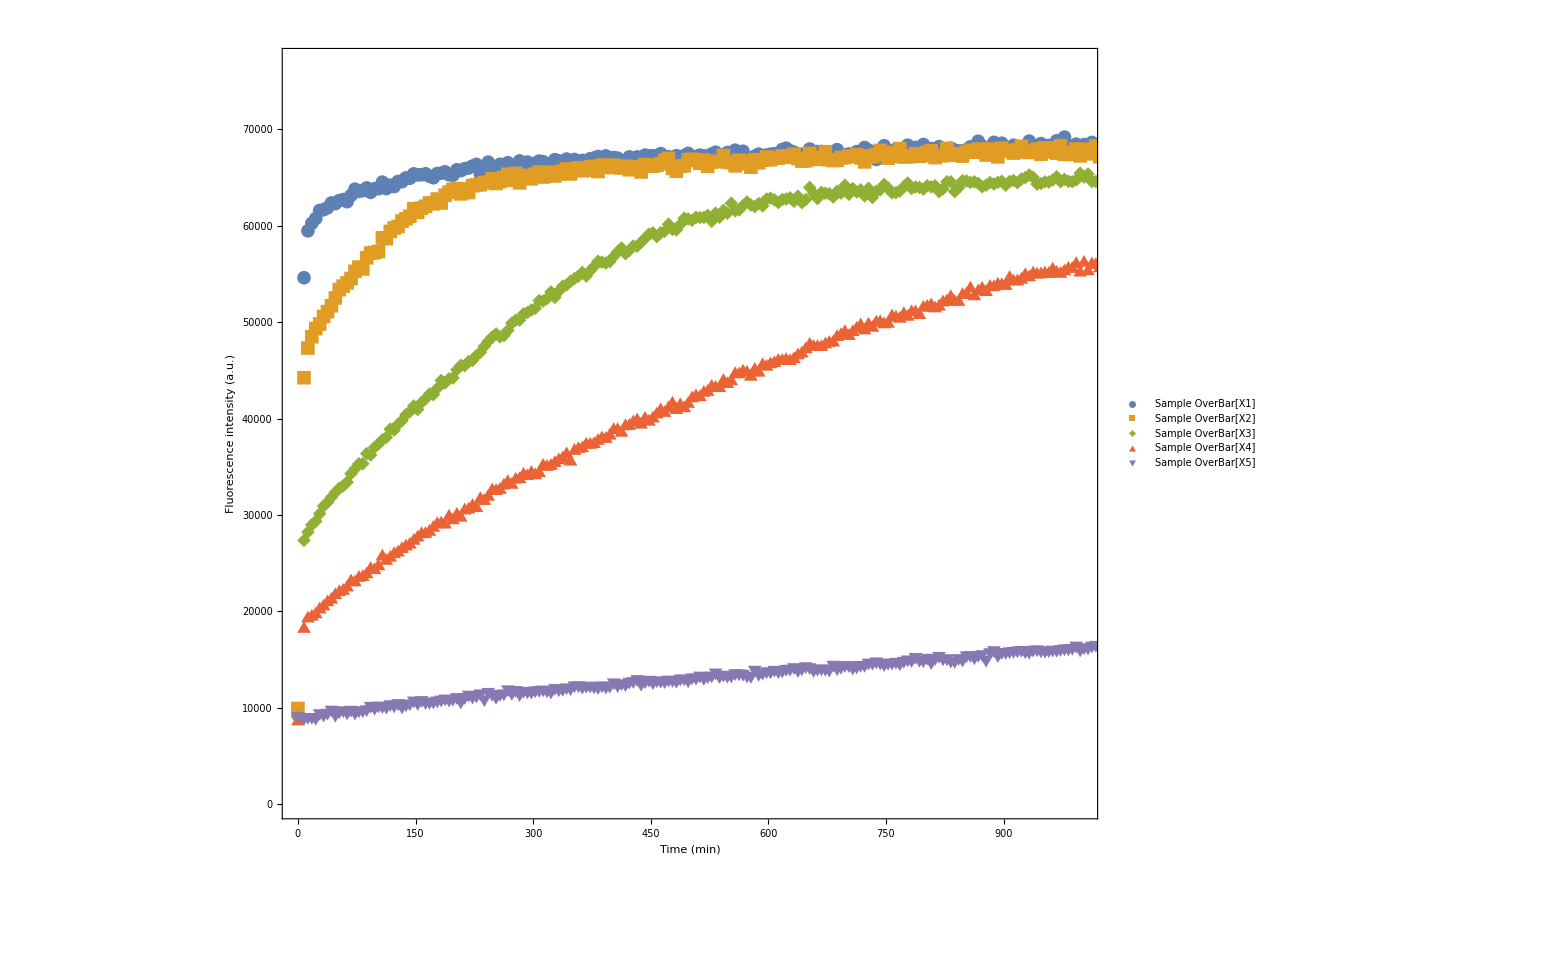

SI\DP_Alexa_norm.pdf

```mathematica
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
list={11,12,24,25,26,27,28,29,30,31,32,33}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[mean[dnormCy[[21;;30]]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\DP_Alexa_norm.pdf",qs]
```

{11,12,24,25,26,27,28,29,30,31,32,33}

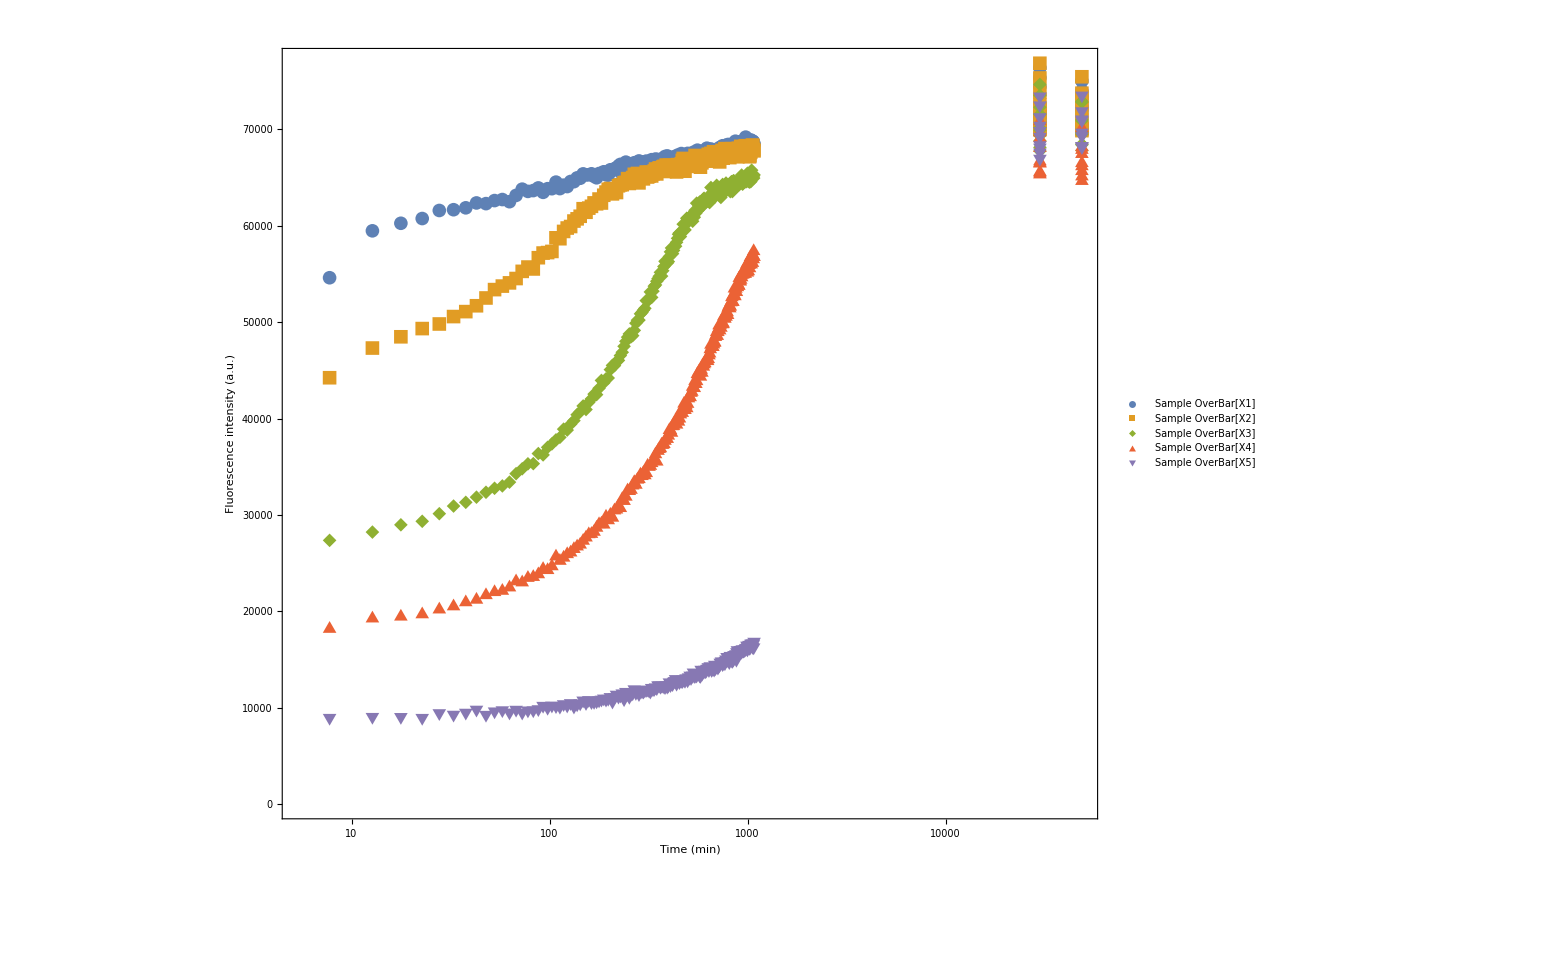

SI\DP_Cy3_long_time.pdf

```mathematica
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
list={11,12,24,25,26,27,28,29,30,31,32,33}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListLogLinearPlot[mean[dnormCy[[21;;30]]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{All,All}]
Export["SI\\DP_Cy3_long_time.pdf",qs]
```

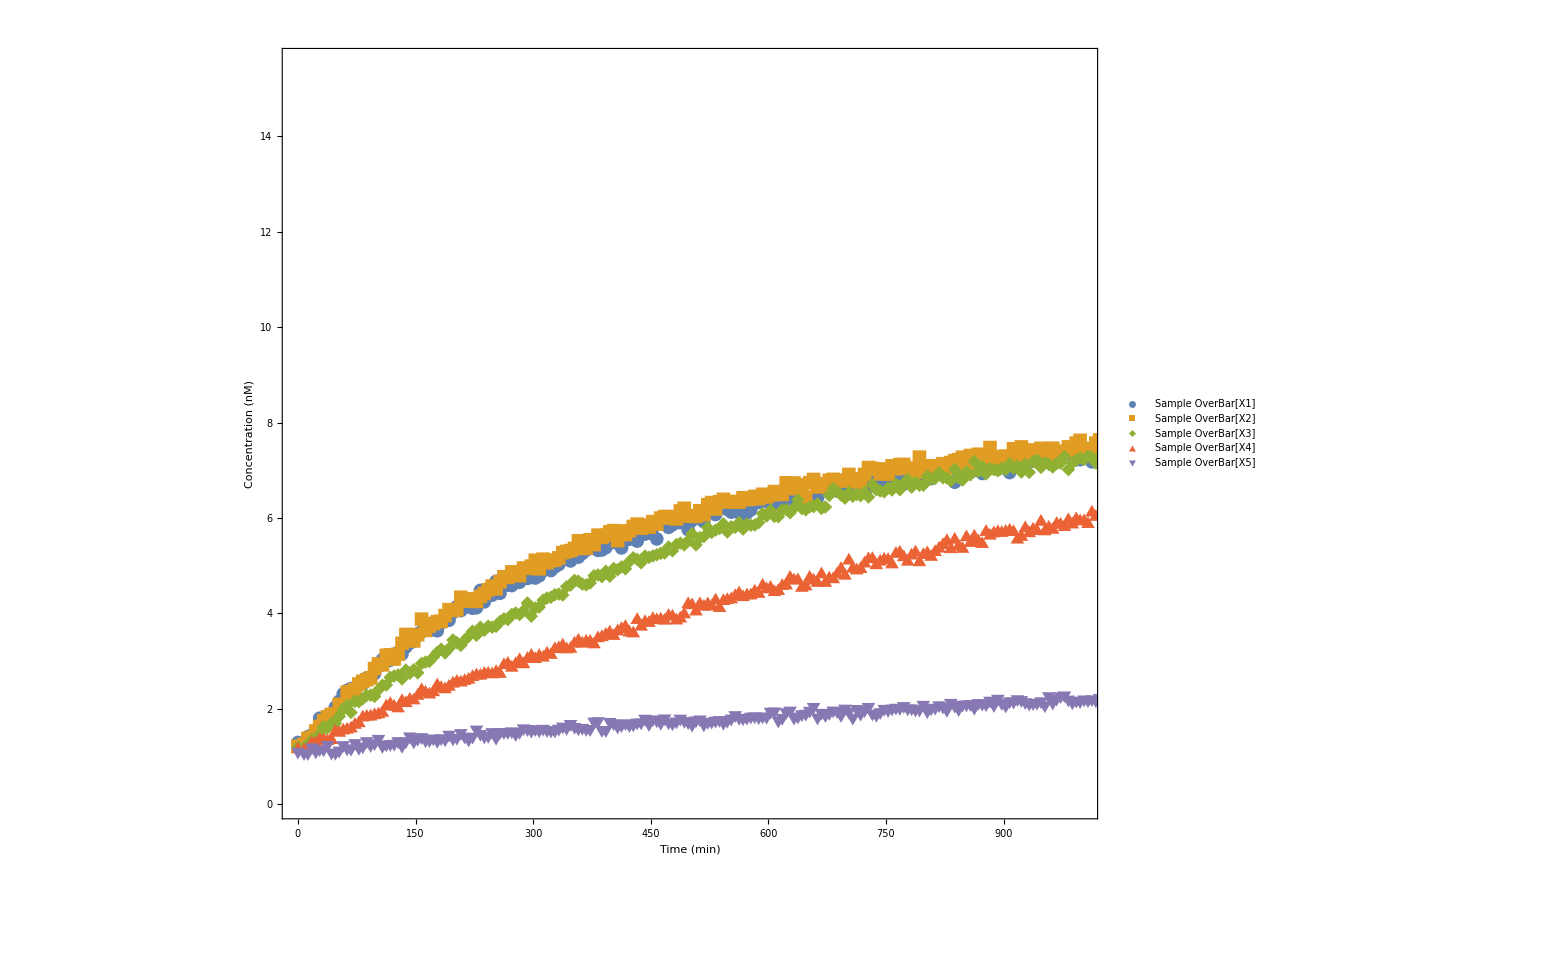

SI\DP_Alexa_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[emp2[[11;;15]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\DP_Alexa_conc.pdf",qs]
```

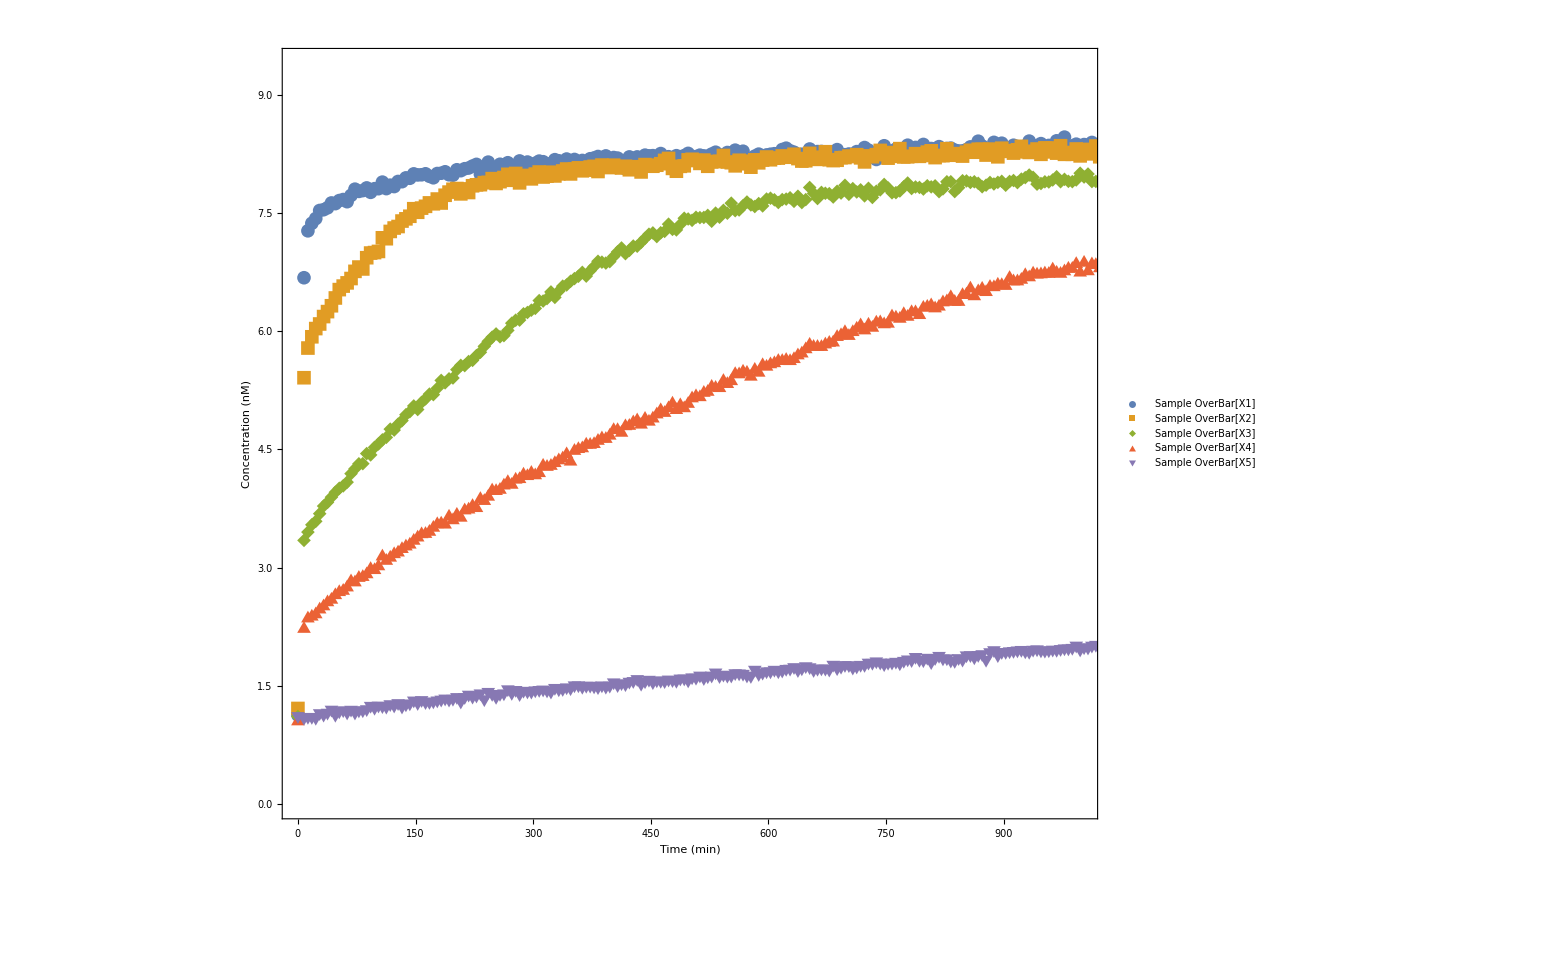

SI\DP_Cy3_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[emp[[11;;15]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\DP_Cy3_conc.pdf",qs]
```